# Rapport - Inlämningsuppgift 2

Dana Ghafour, TIDAB, danagf@ug.kth.se

Sophie Malmberg, TIDAB, sophiema@ug.kth.se

Uppgift 1

## Sammanfattning

### Uppgift

Gör en uppskattning av världens energikonsumtion år 2050.

### Lösning

Vi utgår från datan för världens totala energikonsumtion år 1990-2017 som finns i beskrivningen för inlämningsuppgiften. Vi anpassar sedan en linjär anpassning efter datapunkterna för att göra en uppskattning av konsumtionen fram till år 2050.

### Resultat

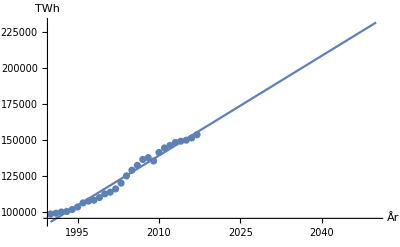

Graf med datapunkter för världens totala energikonsumtion samt en anpassad linjär modell

Svar: Vi uppskattar att världens totala energikonsumtion år 2050 är ungefär 232 000 TWh.

## Kod

```mathematica
totalt={{1990.,98462.371847116},{1991.,98987.38143285},{1992.,99813.54908523199},{1993.,100216.423316547},{1994.,101537.18489717401},{1995.,103296.25934793001},{1996.,106154.70010584098},{1997.,107376.31135546902},{1998.,108022.57284627101},{1999.,109856.69807370701},{2000.,112416.258116246},{2001.,113610.635952175},{2002.,115901.223848704},{2003.,119930.15013616001},{2004.,124960.08846344402},{2005.,128897.75152416898},{2006.,132297.06634468702},{2007.,136405.679742778},{2008.,137662.43593741},{2009.,135324.15543267998},{2010.,141265.10288404},{2011.,144422.53459229},{2012.,146106.05926769998},{2013.,148234.8407671},{2014.,149077.14748530003},{2015.,149790.2224058},{2016.,151341.68784990002},{2017.,153595.6630277}};
```

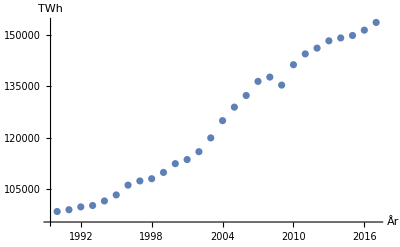

```mathematica
lpTot=ListPlot[totalt, AxesLabel->{"År","TWh"}]
```

```mathematica
{aTot,bTot}={a,b}/.FindFit[totalt,{a(t-1990)+b},{a,b},t]
```

{2314.87,92855.}

```mathematica
eTot[t_]:=aTot(t-1990)+bTot
```

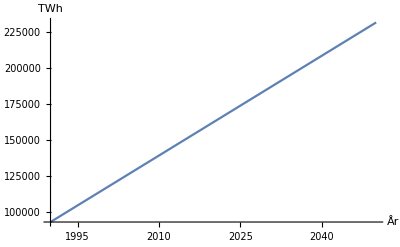

```mathematica
pTot=Plot[eTot[t],{t,1990,2050}, AxesLabel->{"År","TWh"}]
```

```mathematica
Show[lpTot,pTot,PlotRange->{{1990,2050},All}]
```

-Graphics-

```mathematica
eTot[2050]
```

231747.

Uppgift 2

## Sammanfattning

### Uppgift

Uppskatta när olja som energikälla kan ersättas av förnybara energikällor.

### Lösning

Genom att anpassa olika typer av modeller till datapunkterna för respektive energislag kan vi göra en uppskattning av när olja som energikälla kan ersättas av förnybara energikällor. 

Uppskattningen för oljans energiproduktion gör vi genom att skapa en linjär anpassning efter datapunkterna. På samma sätt gör vi en uppskattning av kärnkraften och vattenkraftens energiproduktion. Uppskattningarna för vindkraften och andra förnybara energikällor modelleras med hjälp av andragradsfunktioner. Solkraften modelleras med hjälp av en tredjegradsfunktion.

Genom att addera värdet av förnybara energikällors energiproduktion kan vi jämföra detta värdet med oljans energiproduktion. Vi räknar sedan ut vilket årtal dessa värden är lika stora.

### Resultat

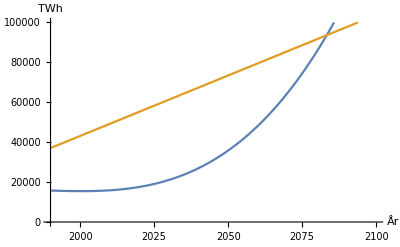

Grafen visar modellerna för olja (gult) och förnybara energikällor (blått).

Svar: Olja som energikälla kan ersättas av förnybara energikällor ungefär år 2083.

## Kod

#### Olja

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

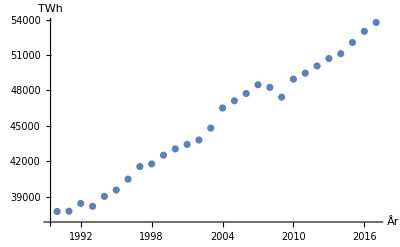

```mathematica
lpO=ListPlot[olja,AxesLabel->{"År","TWh"}]
```

```mathematica
{aO,bO}={a,b}/.FindFit[olja,{a(t-1990)+b},{a,b},t]
```

{606.174,37053.3}

```mathematica
eO[t_]:=aO(t-1990)+bO
```

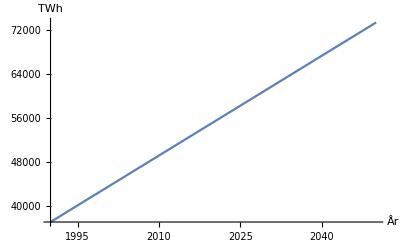

```mathematica
pO=Plot[eO[t],{t,1990,2050},AxesLabel->{"År","TWh"}]
```

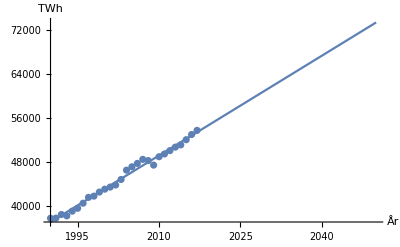

```mathematica
Show[pO,lpO]
```

#### Kärnkraft

```mathematica
karnkraft={{1990.,2000.642591},{1991.,2096.356868},{1992.,2112.277946},{1993.,2185.016841},{1994.,2226.050783},{1995.,2322.592422},{1996.,2407.002623},{1997.,2390.480054},{1998.,2431.571247},{1999.,2524.546817},{2000.,2580.976669},{2001.,2653.821898},{2002.,2696.204132},{2003.,2641.599256},{2004.,2757.124087},{2005.,2769.046942},{2006.,2803.605088},{2007.,2746.479825},{2008.,2737.860822},{2009.,2699.245242},{2010.,2767.507814},{2011.,2651.771616},{2012.,2472.44864},{2013.,2491.705601},{2014.,2541.027341},{2015.,2575.664304},{2016.,2612.83283},{2017.,2635.561104}};
```

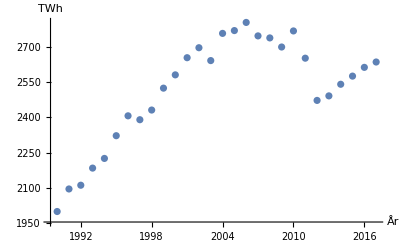

```mathematica
lpK=ListPlot[karnkraft, AxesLabel->{"År","TWh"}]
```

```mathematica
karnkraft1=Take[karnkraft,-18]
```

{{2000.,2580.98},{2001.,2653.82},{2002.,2696.2},{2003.,2641.6},{2004.,2757.12},{2005.,2769.05},{2006.,2803.61},{2007.,2746.48},{2008.,2737.86},{2009.,2699.25},{2010.,2767.51},{2011.,2651.77},{2012.,2472.45},{2013.,2491.71},{2014.,2541.03},{2015.,2575.66},{2016.,2612.83},{2017.,2635.56}}

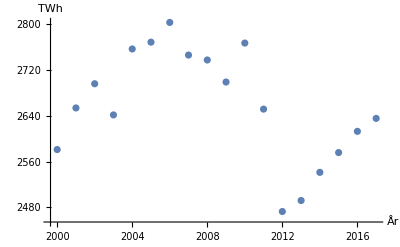

```mathematica
lpKu=ListPlot[karnkraft1, AxesLabel->{"År","TWh"}]
```

```mathematica
{aK,bK}={a,b}/.FindFit[karnkraft1,{a(t-2000)+b},{a,b},t]
```

{-7.80172,2723.79}

```mathematica
eK[t_]:=aK(t-2000)+bK
```

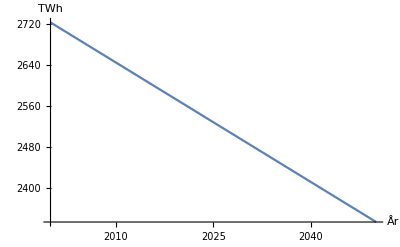

```mathematica
pK=Plot[eK[t],{t,2000,2050}, AxesLabel->{"År","TWh"}]
```

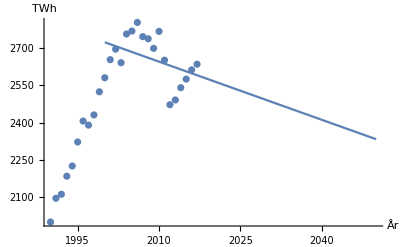

```mathematica
Show[lpK,pK,PlotRange->{{1990,2050},All}]
```

#### Vatten

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

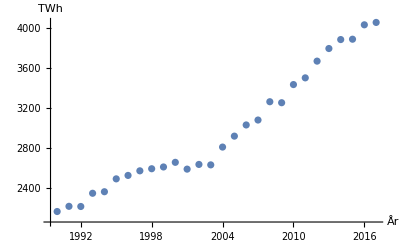

```mathematica
lpV=ListPlot[vatten, AxesLabel->{"År","TWh"}]
```

```mathematica
{aV,bV}={a,b}/.FindFit[vatten,{a(t-1990)+b},{a,b},t]
```

{71.3453,2008.72}

```mathematica
eV[t_]:=aV(t-1990)+bV;
```

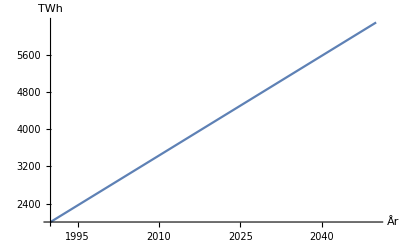

```mathematica
pV=Plot[eV[t],{t,1990,2050},AxesLabel->{"År","TWh"}]
```

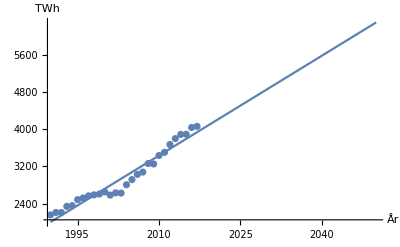

```mathematica
Show[lpV,pV,PlotRange->{{1990,2050},All},AxesLabel->{"År","TWh"}]
```

#### Vind

Obs! Andragradsfunktion

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
```

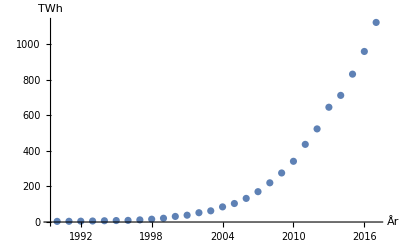

```mathematica
lpVi=ListPlot[vind,AxesLabel->{"År","TWh"}]
```

```mathematica
{aVi,bVi,cVi}={a,b, c}/.FindFit[vind,{a(t-1990)^2 +b(t-1990)+c},{a,b, c},t]
```

{2.67722,-37.846,92.6153}

```mathematica
eVi[t_]:=aVi(t-1990)^2+bVi(t-1990)+cVi
```

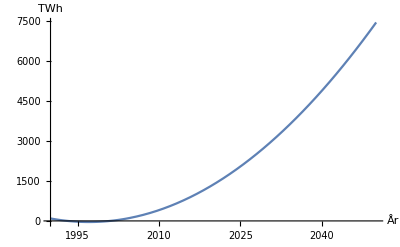

```mathematica
pVi = Plot[eVi[t], {t,1990,2050},AxesLabel->{"År","TWh"}]
```

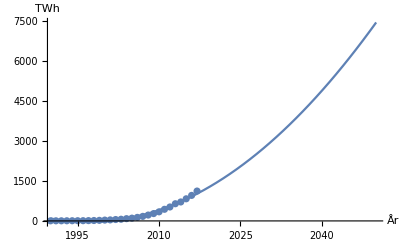

```mathematica
Show[lpVi,pVi,PlotRange->{{1990,2050},All},AxesLabel->{"År","TWh"}]
```

#### Sol

Obs! Tredjegradsfunktion

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

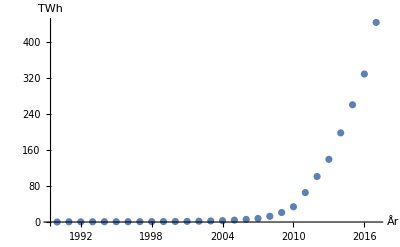

```mathematica
lpS = ListPlot[sol,AxesLabel->{"År","TWh"}]
```

```mathematica
{aS,bS,cS, cD}={a,b, c, d}/.FindFit[sol,{a(t-1990)^2 +b(t-1990)+c + d(t-1990)^3},{a,b, c,d },t]
```

{-2.62951,19.2316,-24.7862,0.0929575}

```mathematica
eSo[t_]:=aS(t-1990)^2+bS(t-1990)+cS + cD(t-1990)^3
```

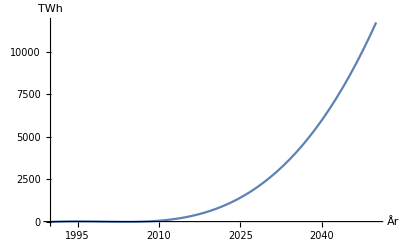

```mathematica
pS = Plot[eSo[t], {t,1990,2050},AxesLabel->{"År","TWh"}]
```

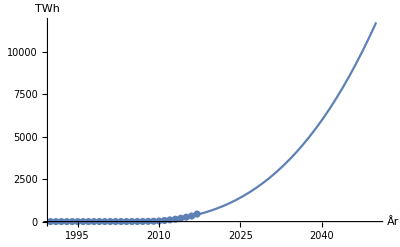

```mathematica
Show[lpS,pS,PlotRange->{{1990,2050},All}]
```

#### Andra förnybara energikällor

Obs! Andragradsfunktion

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

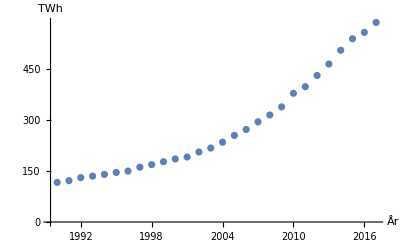

```mathematica
lpA=ListPlot[andrafornybara,AxesLabel->{"År","TWh"}]
```

```mathematica
{aA,bA,cA}={a,b,c}/.FindFit[andrafornybara,{a(t-1990)^2+b(t-1990)+c},{a,b,c},t]
```

{0.719861,-2.28043,131.433}

```mathematica
eA[t_]:=aA(t-1990)^2+bA(t-1990)+cA
```

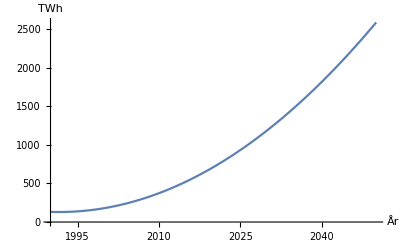

```mathematica
pA=Plot[eA[t],{t,1990,2050},AxesLabel->{"År","TWh"}]
```

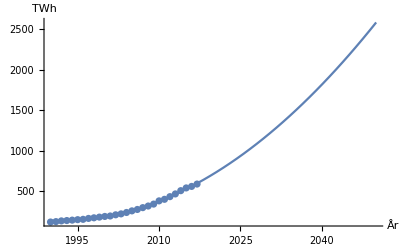

```mathematica
Show[pA,lpA,PlotRange->{{1990,2050},All},AxesLabel->{"År","TWh"}]
```

#### Biobränsle

```mathematica
biobransle={{1990.,11111.11111},{1991.,11242.7549},{1992.,11375.95839},{1993.,11510.74008},{1994.,11647.11865},{1995.,11785.11302},{1996.,11924.74234},{1997.,12066.02598},{1998.,12208.98355},{1999.,12414.05573},{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.70237},{2004.,12159.75217},{2005.,12076.14729},{2006.,11993.11724},{2007.,11910.65806},{2008.,11828.76583},{2009.,11747.43666},{2010.,11666.66667},{2011.,11553.3766},{2012.,11441.18663},{2013.,11330.0861},{2014.,11220.06442},{2015.,11111.11111},{2016.,11003.2158},{2017.,10895.32049}};
```

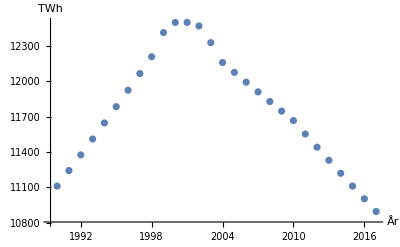

```mathematica
lpB=ListPlot[biobransle,AxesLabel->{"År","TWh"}]
```

```mathematica
biobransle1=Take[biobransle,-18]
```

{{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.7},{2004.,12159.8},{2005.,12076.1},{2006.,11993.1},{2007.,11910.7},{2008.,11828.8},{2009.,11747.4},{2010.,11666.7},{2011.,11553.4},{2012.,11441.2},{2013.,11330.1},{2014.,11220.1},{2015.,11111.1},{2016.,11003.2},{2017.,10895.3}}

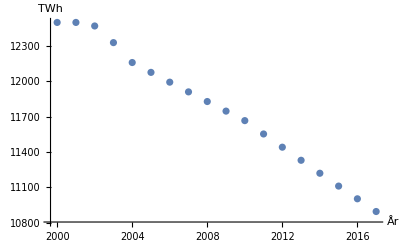

```mathematica
lpB=ListPlot[biobransle1,AxesLabel->{"År","TWh"}]
```

```mathematica
{aB,bB}={a,b}/.FindFit[biobransle1,{a(t-2000)+b},{a,b},t]
```

{-97.5393,12592.2}

```mathematica
eBio[t_]:=aB(t-2000)+bB
```

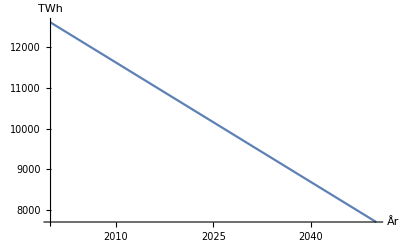

```mathematica
lpBu=Plot[eBio[t],{t,2000,2050}, AxesLabel->{"År","TWh"}]
```

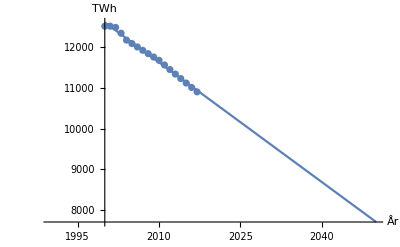

```mathematica
Show[lpBu,lpB,PlotRange->{{1990,2050},All},AxesLabel->{"År","TWh"} ]
```

#### Totalt

```mathematica
eAFo[t_]:=eA[t]+eBio[t]+eSo[t]+eVi[t]+eV[t];
```

```mathematica
pAFo = Plot[{eAFo[t], eO[t]},{t,1990,2100}, PlotRange->{0,100000}, AxesLabel->{"År","TWh"}]
```

-Graphics-

```mathematica
FindRoot[eAFo[t]== eO[t], {t,2090}]
```

{t→2083.33}

Modell för antal TWh för alla förnybara energikällor (biobränslen, sol, vind, vatten, andra förnybara källor) i blått. Jämförs med olja i gult.

Uppgift 3

## Sammanfattning

### Uppgift

Gör en uppskattning av om eller när energikonsumtionen i världen är CO2-fri.

### Lösning

På samma sätt som i Uppgift 2 använder vi matematiska anpassningar för att skapa en modell för varje energislag som kan uppskatta produktionen i framtiden. Till kolkraften anpassas en andragradsfunktion och till naturgasen en linje. Vi adderar värdet för produktionen av de CO2-fria energislagen och jämför det med de övriga energislagens produktion. Sedan räknar vi ut vilket år dessa värden är lika.

### Resultat

Svar: Enligt vår modell beräknas energikonsumtionen i världen bli CO2-fri ungefär år 2240.

## Kod

#### Kol

```mathematica
kol={{1990.,25845.88485},{1991.,25561.41954},{1992.,25478.81089},{1993.,25580.92144},{1994.,25729.64169},{1995.,25867.8533},{1996.,26516.28457},{1997.,26549.71899},{1998.,26351.79429},{1999.,26492.77461},{2000.,27403.94562},{2001.,27851.05371},{2002.,28936.6423},{2003.,31475.58334},{2004.,33656.31109},{2005.,36118.94545},{2006.,37979.81684},{2007.,40143.91171},{2008.,40712.5427},{2009.,40088.33994},{2010.,41932.74507},{2011.,43948.96889},{2012.,44129.62497},{2013.,44953.01385},{2014.,44916.83781},{2015.,43786.8458},{2016.,43101.23216},{2017.,43397.13549}};
```

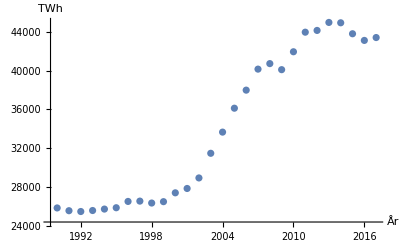

```mathematica
lpKol=ListPlot[kol,AxesLabel->{"År","TWh"}]
```

```mathematica
{aKol,bKol,cKol}={a,b,c}/.FindFit[kol,{a(t-1990)^2+b(t-1990)+c},{a,b,c},t]
```

{11.2092,605.756,23137.6}

```mathematica
eKol[t_]:=aKol(t-1990)^2+bKol(t-1990)+cKol
```

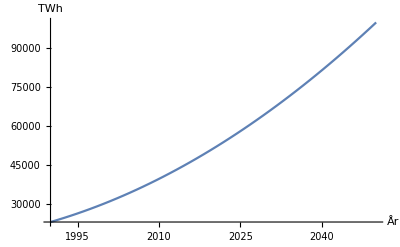

```mathematica
pKol=Plot[eKol[t],{t,1990,2050},AxesLabel->{"År","TWh"}]
```

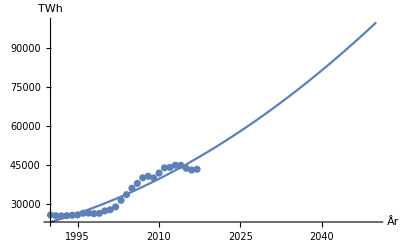

```mathematica
Show[pKol,lpKol,PlotRange->{{1990,2050},All}]
```

#### Naturgas

```mathematica
naturgas={{1990.,19486.64542},{1991.,19984.58677},{1992.,20076.92098},{1993.,20275.09431},{1994.,20405.36342},{1995.,21121.78818},{1996.,22143.41796},{1997.,22082.05319},{1998.,22485.93806},{1999.,23107.57158},{2000.,24019.89227},{2001.,24367.11133},{2002.,25108.12839},{2003.,25769.17552},{2004.,26752.16794},{2005.,27537.09099},{2006.,28347.57835},{2007.,29580.25097},{2008.,30321.37836},{2009.,29477.9263},{2010.,31759.12422},{2011.,32410.44868},{2012.,33270.53388},{2013.,33714.94785},{2014.,33986.84723},{2015.,34741.88349},{2016.,35741.82987},{2017.,36703.96587}};
```

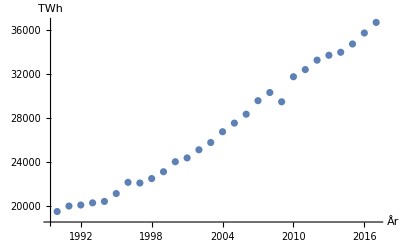

```mathematica
lpNatur = ListPlot[naturgas,AxesLabel->{"År","TWh"}]
```

```mathematica
{aN,bN}={a,b}/.FindFit[naturgas,{a(t-1990)+b},{a,b},t]
```

{665.624,17970.5}

```mathematica
eNatur[t_]:=aN(t-1990)+bN
```

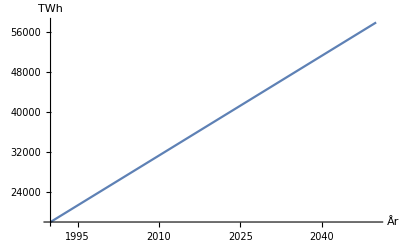

```mathematica
lpNa=Plot[eNatur[t],{t,1990,2050},AxesLabel->{"År","TWh"}]
```

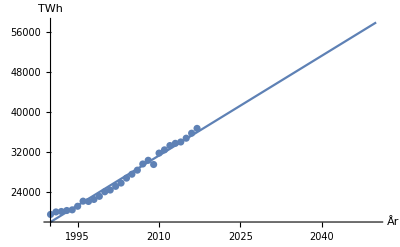

```mathematica
Show[lpNa,lpNatur,PlotRange->{{1990,2050},All},AxesLabel->{"År","TWh"}]
```

```mathematica
ejCO2fri[t_]:=eO[t]+eKol[t]+eNatur[t] + eBio[t] + eA[t]
```

```mathematica
CO2fri[t_]:=eSo[t]+eVi[t]+eV[t]+eK[t]
```

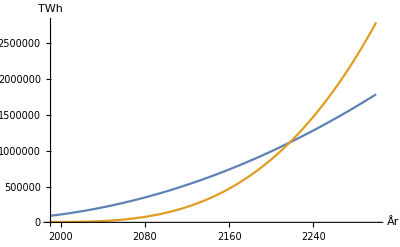

```mathematica
Plot[{ejCO2fri[t],CO2fri[t]},{t,1990,2300},PlotRange->All, AxesLabel->{"År","TWh"}]
```

```mathematica
FindRoot[ejCO2fri[t]==CO2fri[t],{t,2300}]
```

{t→2217.72}

Uppgift 4

## Sammanfattning

### Uppgift

Vilket förnybart energislag uppskattas vara viktigast år 2050?

### Lösning

Vi jämför värdet för antalet TWh/år mellan de olika energikällorna enligt de tidigare framtagna funktionerna i uppgift 2.

### Resultat

Svar: Solenergi uppskattas vara viktigast år 2050 med en produktion på ungefär 11 700 TWh per år. Resterande energislag kommer att ha en produktion mellan 2500-8000 Twh/år vardera.

## Kod

```mathematica
andra50 = eA[2050]
```

2586.1

```mathematica
vatten50 = eV[2050]
```

6289.44

```mathematica
vind50 = eVi[2050]
```

7459.84

```mathematica
vBio = eBio[2050]
```

7715.21

```mathematica
vSol = eSo[2050]
```

11741.7

Uppgift 5

## Sammanfattning

### Uppgift

Besvara frågan: “Vad har val av modell för betydelse?”

### Resultat

Valet av modell påverkar främst funktionens lutning/hastighet och dess acceleration. En linjär modell för att uppskatta energiproduktionen kommer att ha samma lutning oavsett årtal, medan värdet för en andra- och tredjegradsfunktion ökar med en större hastighet ju längre tiden går. Det kan resultera i stora skillnader för vilket värde funktionen får under senare årtal.

Uppgift 6

## Sammanfattning

### Uppgift

Besvara frågan: “Är ovanstående förutsägelser rimliga? Är förutsägelserna rimliga till 2030?”

### Lösning

För att ta reda på om förutsägelserna om den framtida totala energikonsumtionen är rimliga kan vi jämföra två olika modeller. Vi jämför den första modellen (modell 1) i uppgift 1 med våra modeller för de enskilda energislagen (modell 2). Vi adderar alla kurvanpassningar/linjeanpassningar för de individuella energislagen och skapar en graf. Vi jämför även funktionsvärdet för modellerna år 2030.

### Resultat

Vi får ett resultat som visar att båda modellerna resulterar i en liknande total energikonsumtion fram till år 2016. Eftersom modell 2 är exponentiell innebär det att funktionsvärdet ökar kraftigt under de senare årtalen. År 2030 resulterar modell 2 i en energikonsumtion på ungefär 195 000 TWh, medan modell 1) resulterar i en energikonsumtion på ungefär 185 000 TWh. Det skiljer sig alltså ungefär 10 000 TWh mellan resultaten för år 2030, där funktionsvärdet för modell 2 är ungefär 5 procent högre än det för modell 1.

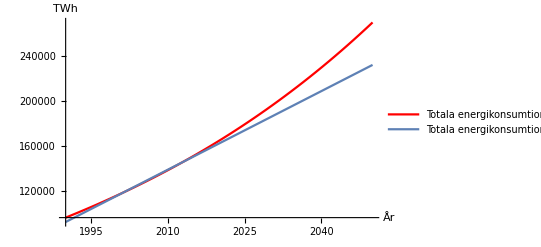

```mathematica
eTotModell[t_]:=eO[t]+eKol[t]+eVi[t]+eNatur[t]+eBio[t]+eA[t]+eSo[t]+eK[t]+eV[t]
p1=Plot[eTotModell[t],{t,1990,2050},PlotStyle->Red, PlotLegends->{"Totala energikonsumtionen (modell 2)"}, AxesLabel->{"År","TWh"}];
p2=Plot[eTot[t],{t,1990,2050},PlotLegends->{"Totala energikonsumtionen (modell 1)"}, AxesLabel->{"År","TWh"}];
Show[p1,p2, PlotRange->Automatic]
```

## Kod

```mathematica
eTotModell[t_]:=eO[t]+eKol[t]+eVi[t]+eNatur[t]+eBio[t]+eA[t]+eSo[t]+eK[t]+eV[t]
p1=Plot[eTotModell[t],{t,1990,2050},PlotStyle->Red, PlotLegends->{"Totala energikonsumtionen (modell 2)"}, AxesLabel->{"År","TWh"}];
p2=Plot[eTot[t],{t,1990,2050},PlotLegends->{"Totala energikonsumtionen (modell 1)"}, AxesLabel->{"År","TWh"}];
Show[p1,p2, PlotRange->Automatic]
```

-Graphics-

```mathematica
eTotModell[2030]
```

194757.

```mathematica
eTot[2030]
```

185450.

Uppgift 7

## Sammanfattning

### Uppgift

Besvara frågan: “Vilka felkällor finns?”

### Resultat

Den främsta felkällan för modellerna är vilken anpassning som används för de olika energislagen. En linjär anpassning resulterar troligtvis i ett helt annat värde för funktionen vid högre värden på årtalen jämfört med en andra- eller tredjegradsfunktion. Det är också svårt att säga om energislagens produktion kommer att utvecklas på samma sätt i framtiden, samt om de påverkas av miljöpolitiska beslut, exempelvis användingen av kärnkraft. En annan osäkerhet över en längre tidsperiod är tillgången på råvaror globalt som kan påverka möjligheterna att producera energi med vissa energislag.

Uppgift 8

## Sammanfattning

### Uppgift

Världens totala energiförbrukning 2021 var 165 319 TWh. Hur stämmer det med er modell? Kommentera!

### Lösning

Vi räknar ut värdet för den totala förbrukningen år 2021 genom att använda funktionen vi fick fram i uppgift 1.

### Resultat

Resultatet för den totala förbrukningen år 2021 borde vara 164 616 TWh enligt vår modell. Det verkliga värdet är ungefär 0,4 procent högre än vår uträkning, vilket gör att modellen kan anses vara relativt exakt.

## Kod

```mathematica
tot21 = eTot[2021]
```

164616.